```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA","Simple_Yukawa_FA.nlo"}]]
```

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA"}]]
```

Patched 2 FeynArts models.

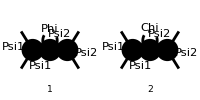

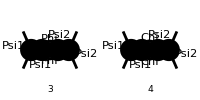

```mathematica
LoopDiags = InsertFields[CreateTopologies[1, 2 -> 2, ExcludeTopologies->{Tadpoles,WFCorrections}],{F[1],-F[1]} -> {F[2],-F[2]}, InsertionLevel->{Particles},ExcludeParticles->{F[1],F[2]},Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[LoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
TotalLoop[0]=Contract/@FCFAConvert[CreateFeynAmp[LoopDiags,Truncated->False,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

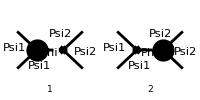

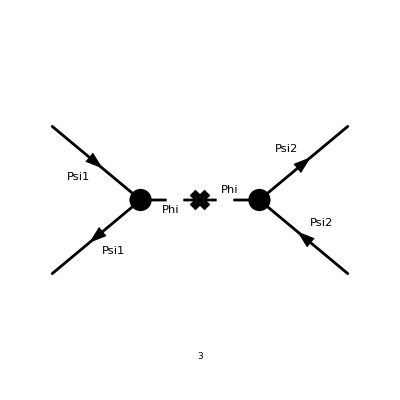

```mathematica
CTDiags = InsertFields[CreateCTTopologies[1, 2 -> 2,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],{F[1],-F[1]} -> {F[2],-F[2]}, InsertionLevel->{Particles}, Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[CTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
```

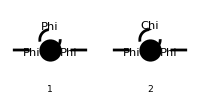

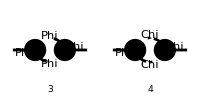

{lambda41/(2 (q^2-mPhi^2)),tau2/(q^2-mChi^2),lambda3^2/(2 (q^2-mPhi^2).((q-p)^2-mPhi^2)),tau1^2/((q^2-mChi^2).((q-p)^2-mChi^2))}

```mathematica
SelfEDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1] -> S[1], InsertionLevel->{Particles},ExcludeParticles->{F[1],F[2]},Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[SelfEDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
SelfEAmp[0]=FCFAConvert[CreateFeynAmp[SelfEDiags ,Truncated->True,PreFactor->1],OutgoingMomenta->{p,p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]//Contract
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
FCClearScalarProducts[];
SP[p,p]=s;
SelfEAmp[1]=SelfEAmp[0]//processLoop;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
CT=(2π)^4(R2$vertlist[[1]][[2]]+UV$vertlist[[5]][[2]])//ReplaceAll[#,{IPL[{S[1]}]->1,IPL[{S[2]}]->1,IPL[{F[1]}]->0,IPL[{F[2]}]->0,FR$Eps->Epsilon,FR$MU->ScaleMu,SP[2,2]->s,FR$deltaZ({Phi,Phi},{{}})->0}]&//Refine[#,Assumptions->mChi>mPhi>0]&;
```

```mathematica
SelfEAmp[2]=-ⅈ(SelfEAmp[1]+CT/.ScaleMu->1)/.Log[Power[a_,b_]]:>b Log[a]//Simplify;
```

```mathematica
SelfEAmp[2]//Expand
```

(π^2 lambda3^2 √(s (s-4 mPhi^2)) log((√(s (s-4 mPhi^2))+2 mPhi^2-s)/(2 mPhi^2)))/(2 s)+1/2 π^2 lambda3^2 log(1/(π mPhi^2))+π^2 lambda3^2 log(mPhi)+(π^3 lambda3^2)/(2 √3)-1/2 ℽ π^2 lambda3^2-1/2 ℽ π^2 lambda41 mPhi^2+π^2 lambda41 mPhi^2 log(mPhi)+1/2 π^2 lambda41 mPhi^2 log(1/(π mPhi^2))-(π^2 tau1^2 √(mPhi^2-4 mChi^2) log((mPhi (√(mPhi^2-4 mChi^2)-mPhi))/(2 mChi^2)+1))/mPhi+(π^2 tau1^2 √(s (s-4 mChi^2)) log((√(s (s-4 mChi^2))+2 mChi^2-s)/(2 mChi^2)))/s+π^2 tau1^2 log(1/(π mChi^2))-ℽ π^2 mChi^2 tau2+2 π^2 mChi^2 tau2 log(mChi)+π^2 mChi^2 tau2 log(1/(π mChi^2))+2 π^2 tau1^2 log(mChi)-ℽ π^2 tau1^2

```mathematica
SelfEAmp[3]=SelfEAmp[2]/.{mPhi->1,mChi->1.5,lambda3->0.1,lambda41->0.02,lambda42->0.2,tau1->0.2,tau2->0.3}
```

(π^2 ((-7.02633+1.19979×10^-17 ⅈ) s+0.24 √((s-9.) s) log(0.222222 (-s+√((s-9.) s)+4.5))+0.03 √((s-4) s) log(1/2 (-s+√((s-4) s)+2))+0.))/(6 s)

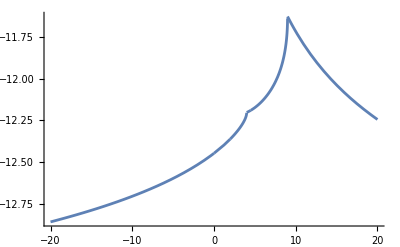

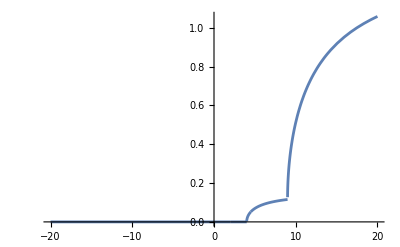

```mathematica
Plot[Re[SelfEAmp[3]],{s,-20,20},MaxRecursion->10]
Plot[Im[SelfEAmp[3]],{s,-20,20},MaxRecursion->10]
```

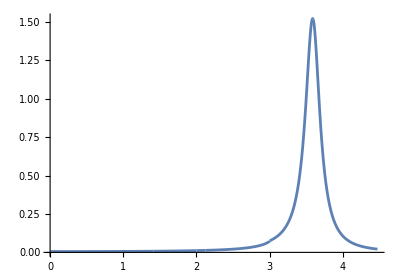

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+SelfEAmp[3]]^-2},{s,-20,20},PlotRange->Full,MaxRecursion->10],AspectRatio->0.7]
```